# 3D Plots

### Continuation ....

```mathematica
RevolutionPlot3D[ Sin[2*x], {x,-2,2}]
```

-Graphics3D-

```mathematica
Manipulate[
RevolutionPlot3D[ Sin[t]* Sin[t^2], {t,0,π } , 
PlotStyle  -> style, 
PlotPoints->p,
Mesh->m],
{{style, Automatic,"Style"}, {Automatic,FaceForm[]}},
{{p, 40,"Points"}, 10, 100 , 1},
{{m,Automatic,"Mesh"}, {All, Full, None}} ]
```

## Other Types of Visualizations

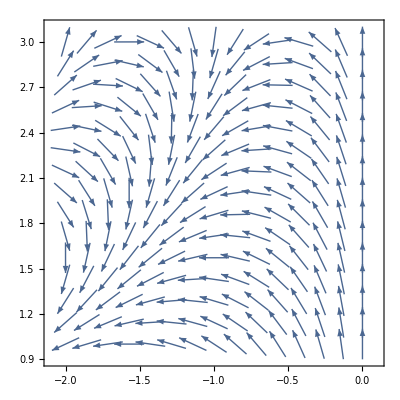

```mathematica
VectorPlot[{Sin[x*y],Cos[x*y]}, {x,-2,0} , {y,1,3}]
```

```mathematica
VectorPlot3D[ {x,y,z} , {x,-1,1} , {y,-1,1}, {z,-1,1}]
```

-Graphics3D-

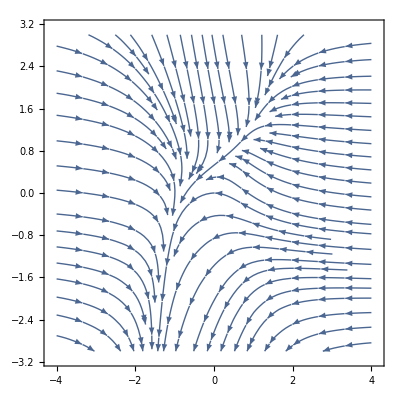

```mathematica
StreamPlot[{-1-x^3+y,x-y^2}, {x,-4,4}, {y,-3,3}]
```

## Graphs

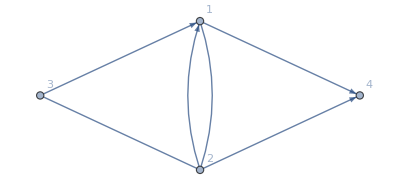

```mathematica
map = { 1<->2, 2 <->3, 3 ->1, 2 ->4,1->4,2->1}; 
Graph[map,VertexLabels->"Name",EdgeLabels->Placed["Name", Tooltip]]
```

```mathematica
ChemicalData["Caffeine","MoleculePlot"]
```

```mathematica
TraditionalForm@
Column[
{"Serotonin Hydrochloride Molecule Mass "  <> ToString[ChemicalData["Cyanamide","MolarMass"]],
ChemicalData["Cyanamide","MoleculePlot"],
}
]
```

Serotonin Hydrochloride Molecule Mass 42.041 grams per mole
-Graphics3D-

```mathematica
ProteinData["SERPINA3","MoleculePlot"]
```

-Graphics3D-